-Graphics-

```mathematica
Mg=1;
R=1;
λ1=1;
Lz=10;
L3=8;
Ueff[t_]:=(Lz-L3*Cos[t]^)2/(2*λ1*Sin[t]^2)+L3^2/(2*λ3)+Mg*R*Cos[t];
```

```mathematica
Ueff[t]
```

Cos[t]+1/2 (10-8 Cos[t])^2 Csc[t]^2

As specified in the problem description, we can ignore the first term in our last expression to get

```mathematica
Ueff[t_]:=(Lz-L3*Cos[t])^2/(2*λ1*Sin[t]^2)+Mg*R*Cos[t];
Ueff[t]
```

Cos[t]+1/2 (10-8 Cos[t])^2 Csc[t]^2

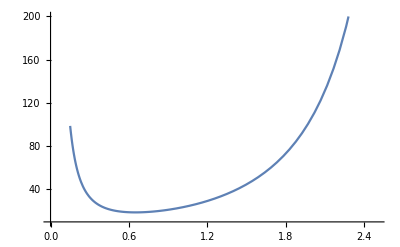

```mathematica
Plot[Ueff[t],{t,.15,2.5},PlotRange->{10,200}]
```